```mathematica
ClearAll["Global`*"]
```

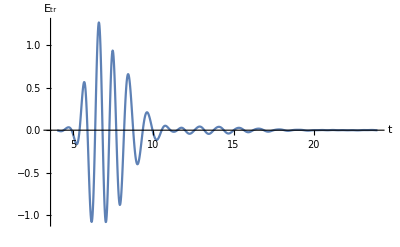

```mathematica
messyData=Import["C:\\Users\\79511\\OneDrive\\Документы\\GitHub\\Labs_Zalipaev\\lab_5\\epsdata.txt"];
lessMessyData=ToExpression@StringReplace[StringSplit[messyData],"e"->"*10^"];
data=Table[{lessMessyData[[i]],lessMessyData[[i+1]]},{i,1,Length[lessMessyData]-1,2}];
tmin=data[[1,1]];
tmax=data[[-1,1]];
ListLinePlot[data,PlotRange->All,AxesLabel->{"t","E_tr"}]
```

```mathematica
(*f[t_]:=Exp[-t^2/(4 Subscript[τ, p]^2)-I Subscript[ω, 0] t]
F[ω_]:=Integrate[Exp[I ω t] f[t],{t,-Infinity,Infinity}][[1]]*
```

```mathematica
z=10^-3;(*detector position*)
c=3*10^8;
factor=N@2 Pi z/c*10^11;
```

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
Etr[t_]:=Interpolation[data][t]
T[f_]:=(F[f,1,1])^(-1)*Integrate[Exp[I (f t-factor)]*Etr[t],{t,tmin,tmax}]
k0=1;
d=1;
Φ[n_]:=(4n)/((n+1)^2 Exp[-I k0 n d]-(n-1)^2 Exp[I k0 n d])-T[f]
(*Eliminate[Φ[n],{n,0}]*)
```

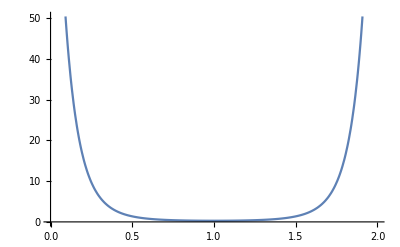

```mathematica
F[f_,τ_,f0_]:=2Sqrt[Pi] τ Exp[-2Pi (f-f0)^2 τ^2]
Plot[(F[f,1,1])^-1,{f,0,2}]
```

```mathematica
interpOrder=3;
timeDomain=Transpose[data][[1]];
discreteExponent[fval_]:=Transpose[{timeDomain,Exp[I (fval t-factor)]/.{t->timeDomain}}];
tc=data[[All,1]];
multipliedFuncValues[fval_]:=Transpose[data][[2]]*Transpose[discreteExponent[fval]][[2]];
multipliedFunction=Transpose[{timeDomain,multipliedFuncValues}];
integral=Integrate[Interpolation[multipliedFunction,InterpolationOrder->3][t],{t,tmin,tmax}]
T[f_]:=(F[f,1,1])^-1*integral
T[1]
```

-0.00144727+0.000421392 ⅈ

-0.000408268+0.000118873 ⅈ

```mathematica
interpOrder=3;
timeDomain=Transpose[data][[1]];
discreteExponent[f_]:=Transpose[{timeDomain,Exp[I (f t-factor)]/.{t->timeDomain}}];
tc=data[[All,1]];
multipliedFuncValues=ParallelTable[Transpose[data][[2]]*Transpose[discreteExponent[i]][[2]],{i,0.4,1,0.1}];
multipliedFunction=ParallelTable[Transpose[{timeDomain,multipliedFuncValues[[i]]}],{i,1,Length[multipliedFuncValues]}];
integral=ParallelTable[Integrate[Interpolation[multipliedFunction[[i]],InterpolationOrder->3][t],{t,tmin,tmax}],{i,1,Length[multipliedFunction]}]
```

{0.000691297+0.000388121 ⅈ,0.000205064+0.000123553 ⅈ,0.000768881+0.000503627 ⅈ,-0.000143013+0.00110587 ⅈ,-0.000322079+0.000417316 ⅈ,-0.000352031+0.000997174 ⅈ,-0.00144727+0.000421392 ⅈ}